```mathematica
SetDirectory[NotebookDirectory[]];
```

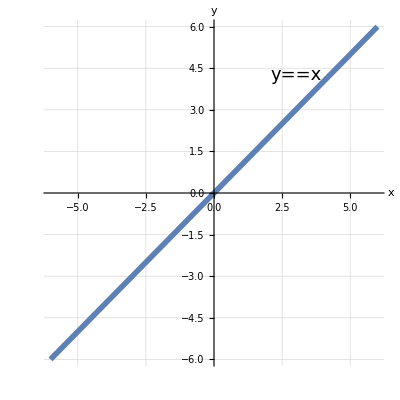

```mathematica
Plot[x,{x,-6,6},PlotStyle->{Thickness[0.01]},GridLines->Automatic,AxesStyle->Directive[16],AxesLabel->{x,y},AspectRatio->1,
Epilog->Text[Style[TraditionalForm[HoldForm[y==x]],18],{3,4.25}]]
Export[{"identity.pdf","identity.svg"},%];
```

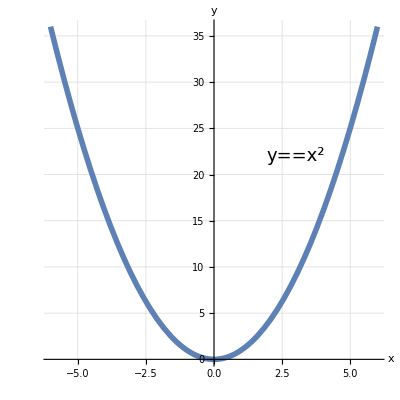

```mathematica
Plot[x^2,{x,-6,6},PlotStyle->{Thickness[0.01]},GridLines->Automatic,AxesStyle->Directive[16],AxesLabel->{x,y},AspectRatio->1,
Epilog->Text[Style[TraditionalForm[HoldForm[y==x^2]],18],{3,22}]]
Export[{"squaring.pdf","squaring.svg"},%];
```

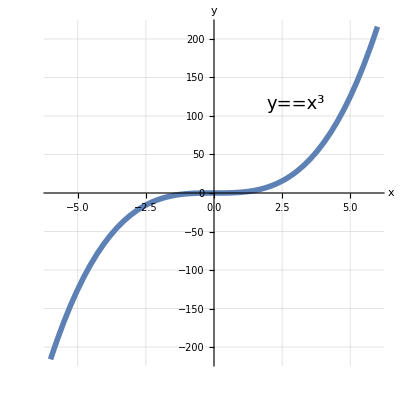

```mathematica
Plot[x^3,{x,-6,6},PlotStyle->{Thickness[0.01]},GridLines->Automatic,AxesStyle->Directive[16],AxesLabel->{x,y},AspectRatio->1,Epilog->Text[Style[TraditionalForm[HoldForm[y==x^3]],18],{3,115}]]
Export[{"cubing.pdf","cubing.svg"},%];
```

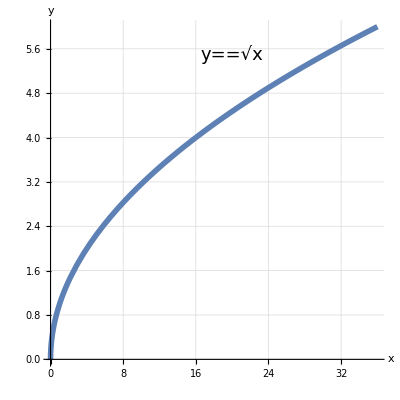

```mathematica
Plot[Sqrt[x],{x,0,36},PlotStyle->{Thickness[0.01]},GridLines->Automatic,AxesStyle->Directive[16],AxesLabel->{x,y},AspectRatio->1,
Epilog->Text[Style[TraditionalForm[HoldForm[y==Sqrt[x]]],18],{20,5.5}]]
Export[{"sqrt.pdf","sqrt.svg"},%];
```

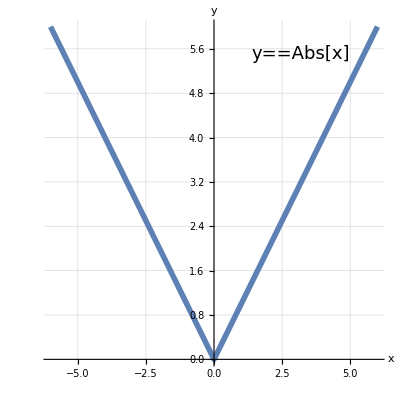

```mathematica
Plot[Abs[x],{x,-6,6},PlotStyle->{Thickness[0.01]},GridLines->Automatic,AxesStyle->Directive[16],AxesLabel->{x,y},AspectRatio->1,Epilog->Text[Style[TraditionalForm[HoldForm[y==Abs[x]]],18],{3.2,5.5}]]
Export[{"abs.pdf","abs.svg"},%];
```

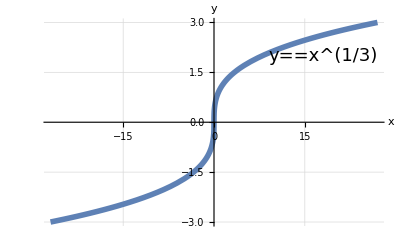

```mathematica
Plot[CubeRoot[x],{x,-27,27},PlotStyle->{Thickness[0.01]},GridLines->Automatic,AxesStyle->Directive[16],AxesLabel->{x,y},Epilog->Text[Style[TraditionalForm[HoldForm[y==CubeRoot[x]]],18],{18,2}]]
Export[{"cuberoot.pdf","cuberoot.svg"},%];
```

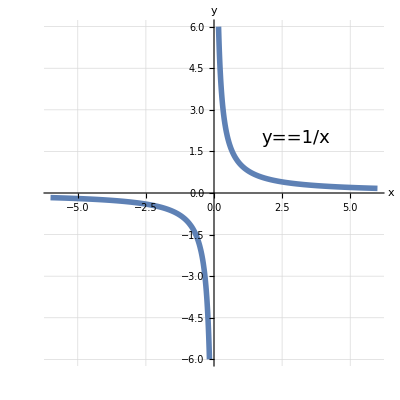

```mathematica
Plot[1/x,{x,-6,6},PlotStyle->{Thickness[0.01]},GridLines->Automatic,AxesStyle->Directive[16],AxesLabel->{x,y},AspectRatio->1,PlotRange->{{-6,6},{-6,6}},Epilog->Text[Style[TraditionalForm[HoldForm[y==1/x]],18],{3,2}]]
Export[{"reciprocal.pdf","reciprocal.svg"},%];
```